```mathematica
DemoValue[k_]:=allGraphs[k,"colofour"]/.demoValues
```

```mathematica
Table[Labeled [allGraphs[k,"graph"],{allGraphs[k,"colofournull"],k,(allGraphs[k,"colofour"]/.demoValues)}],{k,Sort[nullAtomKeys,DemoValue[#1]>DemoValue[#2]&]}]
```

{-Graphics-{p1x2x3x4x5,0,3728},-Graphics-{p1x2x35x4,3,3000},-Graphics-{p1x24x3x5,81,2852},-Graphics-{p1x25x3x4,27,2852},-Graphics-{p13x2x4x5,6561,2640},-Graphics-{p14x2x3x5,2187,2616},-Graphics-{p1x2x3x45,1,2520},-Graphics-{p1x2x34x5,9,2488},-Graphics-{p15x2x3x4,729,2384},-Graphics-{p12x3x4x5,19683,2360},-Graphics-{p1x23x4x5,243,2348},-Graphics-{p1x24x35,84,2324},-Graphics-{p14x2x35,2190,2120},-Graphics-{p13x24x5,6642,2050},-Graphics-{p13x25x4,6588,2038},-Graphics-{p14x25x3,2214,1996},-Graphics-{p1x25x34,36,1940},-Graphics-{p12x35x4,19686,1924},-Graphics-{p15x24x3,810,1848},-Graphics-{p13x2x45,6562,1772},-Graphics-{p14x23x5,2430,1682},-Graphics-{p12x34x5,19692,1598},-Graphics-{p15x2x34,738,1596},-Graphics-{p1x23x45,244,1590},-Graphics-{p12x3x45,19684,1558},-Graphics-{p15x23x4,972,1500},-Graphics-{p1x245x3,109,1292},-Graphics-{p1x2x345,13,1280},-Graphics-{p1x235x4,273,1268},-Graphics-{p135x2x4,7293,1112},-Graphics-{p145x2x3,2917,1112},-Graphics-{p1x234x5,333,1108},-Graphics-{p124x3x5,21951,1060},-Graphics-{p123x4x5,26487,980},-Graphics-{p125x3x4,20439,980},-Graphics-{p134x2x5,8757,976},-Graphics-{p13x245,6670,912},-Graphics-{p14x235,2460,894},-Graphics-{p124x35,21954,870},-Graphics-{p135x24,7374,870},-Graphics-{p12x345,19696,796},-Graphics-{p134x25,8784,746},-Graphics-{p15x234,1062,712},-Graphics-{p145x23,3160,702},-Graphics-{p125x34,20448,672},-Graphics-{p123x45,26488,628},-Graphics-{p1x2345,364,264},-Graphics-{p1245x3,22708,230},-Graphics-{p1345x2,9490,224},-Graphics-{p1235x4,27246,186},-Graphics-{p1234x5,28764,182},-Graphics-{p12345,29524,0}}

```mathematica
ineqsn=Table[allGraphs[k,"comp"][allGraphs[k,"colofournull"],0],{k,Keys[allGraphs]}];Length[ineqsn]
```

1895

```mathematica
countDone=0;ineqsElim2=Monitor[Simplify[Fold[And,ineqsn],Trig->False,ComplexityFunction->MyLeafCount,Assumptions->atomFacts],countDone];Length[ineqsElim2]
```

1805

```mathematica
Map[#[[0]]&,AndToTable[Select[ineqsElim2,Length[ListofVars[#]]==1&]]]//Tally
```

{{Greater,46},{GreaterEqual,5},{Equal,1}}

```mathematica
Select[ineqsElim2,Length[ListofVars[#]]==1&&ToString[#[[0]]]≠"Greater"&]/.repcolofournullgraph2
```

-Graphics-p1234x528764≥0&&-Graphics-p1234529524==0&&-Graphics-p1235x427246≥0&&-Graphics-p1245x322708≥0&&-Graphics-p1345x29490≥0&&-Graphics-p1x2345364≥0

```mathematica
usedNodes=VertexList[Graph[Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsElim2,Length[ListofVars[#]]==2&]]]]]
```

{p123x4x5,p123x45,p124x3x5,p124x35,p125x3x4,p125x34,p12x3x4x5,p12x34x5,p12x35x4,p12x3x45,p1x2x3x4x5,p1x2x34x5,p1x2x345,p12x345,p1x2x35x4,p1x2x3x45,p134x2x5,p134x25,p135x2x4,p135x24,p13x2x4x5,p13x24x5,p13x25x4,p13x2x45,p1x24x3x5,p1x245x3,p13x245,p1x25x3x4,p145x2x3,p145x23,p14x2x3x5,p14x23x5,p14x25x3,p14x2x35,p1x23x4x5,p1x235x4,p14x235,p15x2x3x4,p15x23x4,p15x24x3,p15x2x34,p1x234x5,p15x234,p1x23x45,p1x24x35,p1x25x34}

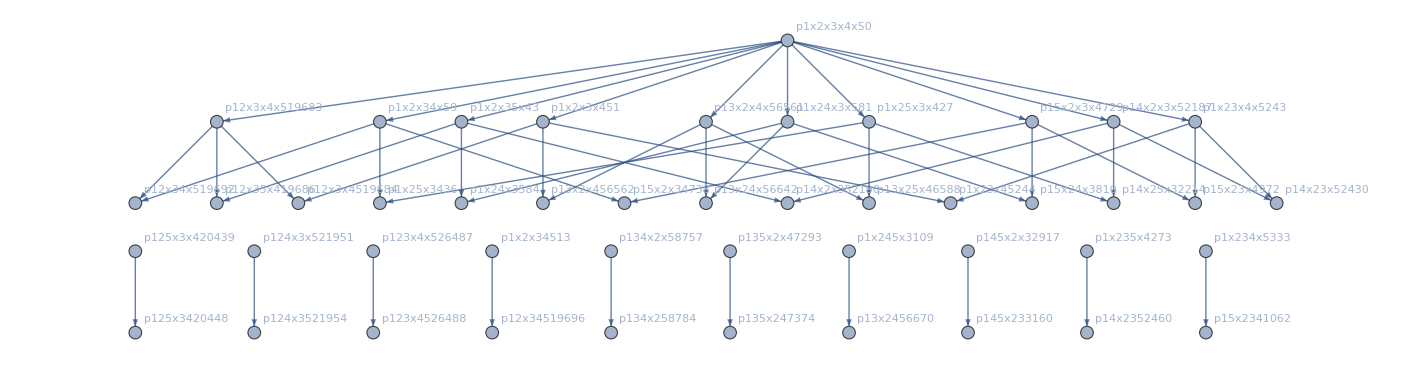

```mathematica
Graph[Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsElim2,Length[ListofVars[#]]==2&]]],VertexLabels->Table[v->(v/.repcolofournullgraph2),{v,usedNodes}]]
```

```mathematica
Select[nullAtomSymbols,!MemberQ[usedNodes,#]&]/.repcolofournullgraph2
```

{-Graphics-p1x2345364,-Graphics-p1345x29490,-Graphics-p1245x322708,-Graphics-p1235x427246,-Graphics-p1234x528764,-Graphics-p1234529524}

```mathematica
MobiusGraph2[key_]:=Block[{form=allGraphs[key,"colofournull"], vars, blocks=Association[],c,edges,set, found=Association[]},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[nullAtomKeys,allGraphs[#,"colofournull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[to[[1]],from[[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
Graph[vars,edges,VertexLabels->Table[n->Tooltip[Rotate[(TableForm[{n,Style[Coefficient[form,n],Bold,Blue]},TableAlignments->Center]),Pi/4],found[n,"graph"]],{n,vars}],ImageSize->600,GraphLayout->"LayeredDigraphEmbedding"]
]
```

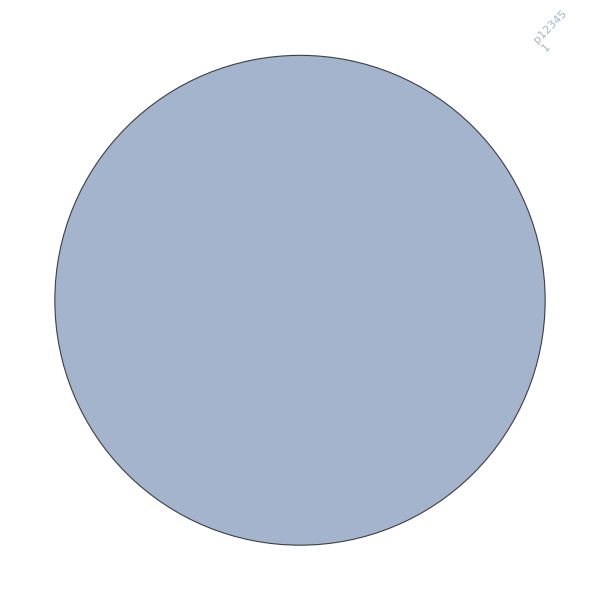

```mathematica
MobiusGraph2[29524]
```